# Fertility And Development

Written by Mark Lauer, August 30th, 2009
Last updated September 24th, 2009
This program is hereby released to the public domain for any purpose.

This notebook generates graphics from the data used in the paper:
Mikko Myrskylä, Hans-Peter Kohler & Francesco C. Billari (2009)
"Advances in development reverse fertility declines"
Nature 460, 741-743 (6 August 2009) | doi:10.1038/nature08230
http://www.nature.com/nature/journal/v460/n7256/full/nature08230.html

## Import Data

Download and import the data

```mathematica
dataurl = "http://www.nature.com/nature/journal/v460/n7256/extref/nature08230-s2.zip";data = First[Import[dataurl, "*"]];
TableForm[data[[Range[5], Range[10]]]]
```

country | HDI.1975 | HDI.1976 | HDI.1977 | HDI.1978 | HDI.1979 | HDI.1980 | HDI.1981 | HDI.1982 | HDI.1983
Albania |  |  |  |  |  | 0.731273 | 0.734932 | 0.737146 | 0.738452
Algeria | 0.565067 | 0.570966 | 0.575103 | 0.581995 | 0.587976 | 0.590365 | 0.593946 | 0.599331 | 0.605605
Angola | 0.427032 | 0.427252 | 0.427463 | 0.428155 | 0.428839 | 0.429516 | 0.424447 | 0.422965 | 0.423151
Argentina | 0.796896 | 0.796294 | 0.800532 | 0.798749 | 0.804949 | 0.807989 | 0.805496 | 0.80343 | 0.805606

Extract and remove the list of countries and column headings, then report the length of each

```mathematica
countrylist = Rest[data[[All,1]]];
headinglist = Rest[data[[1]]];
data = Drop[data, 1, 1];TableForm[{{"Countries: ",Length[countrylist]},{"Columns: ", Length[headinglist]}}]
```

Countries:  | 143
Columns:  | 124

A function to parse column headings and define corresponding Mathematica functions from the values.
For example, "HDI.1975" leads to defining HDI[countryname, 1975]

```mathematica
Store[value_, {country_Integer, columnname_Integer}] :=
Module[{type, year},
{type, year} = StringSplit[headinglist[[columnname]], "."];
(Symbol[type][countrylist[[country]], ToExpression[year]]) = If[NumberQ[value], value, Missing[]]
]
```

Apply this across all the data

```mathematica
MapIndexed[Store, data, {2}];
```

Check this with a couple of plots

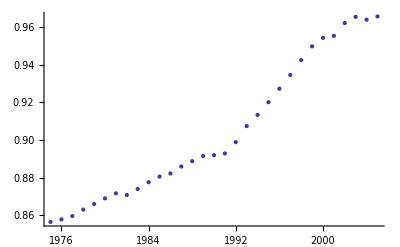

```mathematica
ListPlot[Table[{y, HDI["Australia", y]}, {y, 1975, 2005}]]
```

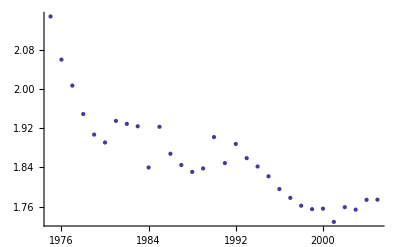

```mathematica
ListPlot[Table[{y, TFR["Australia", y]}, {y, 1975, 2005}]]
```

Generate a scatter plot of all countries' TFR against HDI in 1975 and 2005

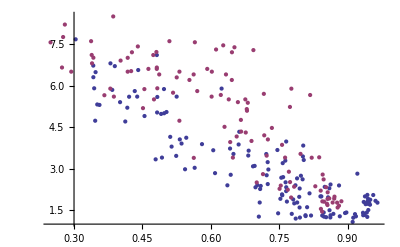

```mathematica
ListPlot[{
{HDI[#, 2005], TFR[#, 2005]}& /@ countrylist, 
{HDI[#, 1975], TFR[#, 1975]}& /@ countrylist} , PlotRange -> All
]
```

Generate a similar plot, but with distorted axes, as the paper does, to make differences at low fertility and high development look much more significant

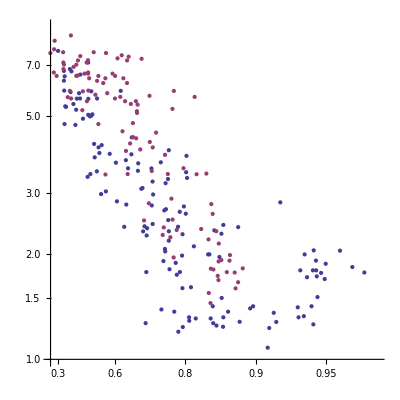

```mathematica
ListLogPlot[{
{-Log[1-HDI[#, 2005]], TFR[#, 2005]}& /@ countrylist, 
{-Log[1-HDI[#, 1975]], TFR[#, 1975]}& /@ countrylist} , Ticks -> {{-Log[1-#], #}& /@ {0.3, 0.6, 0.8, 0.9, 0.95}, Automatic},
PlotRange -> {{-Log[1-0.25], 3.5}, {1, 9}},
AspectRatio -> 1
]
```

## Match Countries To Mathematica Country Data

Define an equivalent list of countries using Mathematica names by expanding some abbreviations and removing spaces

```mathematica
canonicallist = (countrylist /.{"USA" -> "UnitedStates", "Congo, Dem. Rep." -> "DemocraticRepublicCongo","Congo, Rep." -> "RepublicCongo", "Cote d'Ivoire" -> "IvoryCoast", "Kyrgyz Republic" -> "Kyrgyzstan", "NL" -> "Netherlands", "S. Korea" -> "SouthKorea", "Slovak Republic" -> "Slovakia", "Trinidad and Tobago" -> "TrinidadTobago",
"Lao" -> "Laos", x_String :> StringReplace[x, {" " -> ""}]});
```

Check that every country in the data matches one in Mathematica

```mathematica
Complement[canonicallist, CountryData["Countries"]]=={}
```

True

## Key Functions

Define (self-cacheing) function to map countries to the Mathematica names using the list

```mathematica
CanonicalName[country_String] :=
(CanonicalName[country] = canonicallist[[First[First[Position[countrylist, country]]]]])
```

Check this for three countries

```mathematica
CanonicalName /@ {"USA", "New Zealand", "United Kingdom"}
```

{UnitedStates,NewZealand,UnitedKingdom}

Get list of continents for countries

```mathematica
continentslist = Union[CountryData[CanonicalName[#], "Continent"]& /@ countrylist]
```

{Africa,Asia,Europe,NorthAmerica,Oceania,SouthAmerica}

Define (self-cacheing) function to map countries to continents

```mathematica
ContinentOf[country_String] :=
(ContinentOf[country] = CountryData[CanonicalName[country], "Continent"])
```

Check this for four countries

```mathematica
ContinentOf /@ {"USA", "China", "Israel", "Australia"}
```

{NorthAmerica,Asia,Asia,Oceania}

Define ColourOf[] function from continents to colours by splitting the (reversed) DarkRainbow spectrum,
then display all values

```mathematica
MapThread[Set, {ColourOf /@ Reverse[continentslist], ColorData["DarkRainbow"]/@ (Range[Length[continentslist]]/Length[continentslist])}];
Style[#, FontColor -> ColourOf[#]]& /@ continentslist
```

{Africa,Asia,Europe,NorthAmerica,Oceania,SouthAmerica}

Define (self-cacheing) function to map countries to their populations according to Mathematica

```mathematica
PopulationOf[country_String] :=
(PopulationOf[country] = CountryData[CanonicalName[country], "Population"])
```

Check this for four countries

```mathematica
PopulationOf /@ {"USA", "China", "Israel", "Australia"}
```

{3.02841×10^8,1.29801×10^9,6.80999×10^6,2.05304×10^7}

## Animated Charts

Define function to plot a bubble chart of Total Fertility Rate against Human Development Index for a given year.  Bubble sizes are determined by population, colours by continent.

```mathematica
SnapshotChart[year_Integer, chartoptions___] :=
BubbleChart[{
(* Ensure legend appears in fixed order by "plotting" continents *)
Legended[Style[{0,0, 1}, ColourOf[#]], Style[#, Small]]& 
/@ continentslist,
(* Add bubble for each country *) 
Style[
(* On mouse-over, display country names *)
Tooltip[
{HDI[#, year], TFR[#, year], PopulationOf[#]},
#],
ColourOf[ContinentOf[#]]
]& /@ countrylist},
chartoptions,
BubbleSizes -> {0.01, 0.15}, PlotRange -> {{0.2, 1.0}, {0.8, 9}},
FrameLabel -> {"Human Development Index", "Total Fertility Rate"}, PlotLabel -> ToString[year]
]
```

Check this for one year

```mathematica
SnapshotChart[2002]
```

-Graphics--Graphics- | Africa
-Graphics- | Asia
-Graphics- | Europe
-Graphics- | NorthAmerica
-Graphics- | Oceania
-Graphics- | SouthAmerica

Use Mathematica's built in dynamic graphics to view animation through time

```mathematica
Animate[SnapshotChart[y],{y, 1975, 2005, 1}, AnimationRunning -> False, DisplayAllSteps -> True]
```

Generate an animated GIF of all thirty years 
(Note: mouse-over will no longer work outside Mathematica)

```mathematica
Export["FertilityAndDevelopment.gif", Table[SnapshotChart[y], {y, 1975, 2005, 1}], ImageSize -> 440]
```

FertilityAndDevelopment.gif

Generate an animated GIF of all thirty years, zooming in to region with advanced countries 
(Note: mouse-over will no longer work outside Mathematica)

```mathematica
Export["FertilityAndDevelopmentDetail.gif", Table[
SnapshotChart[y, PlotRange -> {{0.7, 1.0}, {0.8, 4}}],
 {y, 1975, 2005, 1}], ImageSize -> 440]
```

FertilityAndDevelopmentDetail.gif

## Trajectory Plots

Use the threshold found by the paper as the HDI level at which TFR changes direction

```mathematica
bouncethreshold = 0.86;
```

Find countries which reach or exceed this threshold at some point in available data

```mathematica
advanced = Select[countrylist, 
(Max[
DeleteCases[Table[HDI[#, i], {i, 1975, 2005}],_Missing]
]≥ bouncethreshold)&]
```

{Argentina,Australia,Austria,Belgium,Canada,Cyprus,Czech Republic,Denmark,Estonia,Finland,France,Germany,Greece,Hungary,Iceland,Ireland,Israel,Italy,Japan,S. Korea,Kuwait,Luxembourg,Malta,NL,New Zealand,Norway,Poland,Portugal,Slovenia,Spain,Sweden,Switzerland,United Arab Emirates,United Kingdom,USA}

Define a function to determine the first year in which a country's HDI exceeds a given threshold

```mathematica
ReferenceYear[country_String, developmentthreshold_Real] :=
Min[
Select[Range[1975, 2005], 
(HDI[country, #]≥ developmentthreshold)&]
]
```

Check this function using the paper's threshold for all advanced countries

```mathematica
TableForm[SortBy[
{#, ReferenceYear[#, bouncethreshold]}& /@ advanced,
Last]]
```

Canada | 1975
Denmark | 1975
NL | 1975
Norway | 1975
Sweden | 1975
Switzerland | 1975
USA | 1975
France | 1976
Japan | 1976
Australia | 1978
Belgium | 1978
Finland | 1978
Iceland | 1978
Austria | 1980
Italy | 1981
New Zealand | 1982
Spain | 1982
United Kingdom | 1982
Germany | 1983
Luxembourg | 1984
Israel | 1985
Ireland | 1990
Greece | 1992
Cyprus | 1995
Portugal | 1997
S. Korea | 1997
Slovenia | 1997
Czech Republic | 2001
Malta | 2001
Kuwait | 2003
United Arab Emirates | 2004
Argentina | 2005
Estonia | 2005
Hungary | 2005
Poland | 2005

Define a function to return the time series of TFR for a given country beginning in its reference year (measured as absolute difference from the TFR in the reference year).

```mathematica
TFRSeriesFromReference[country_String, threshold_Real]:=
If[ReferenceYear[country, threshold]>2005, 
(* Return empty series when HDI never reached threshold *)
{},
Table[TFR[country, y], {y, ReferenceYear[country, threshold], 2005}]-TFR[country, ReferenceYear[country, threshold]]
]
```

Check this function for Australia

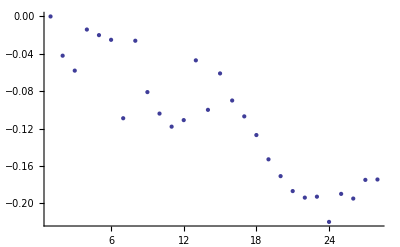

```mathematica
ListPlot[TFRSeriesFromReference["Australia", bouncethreshold]]
```

Define a reasonable colour scheme

```mathematica
stylescheme = Reverse[ColorData["DarkRainbow"]/@ (Range[Length[advanced]]/Length[advanced])];
```

Build a chart of these time series for all advanced countries

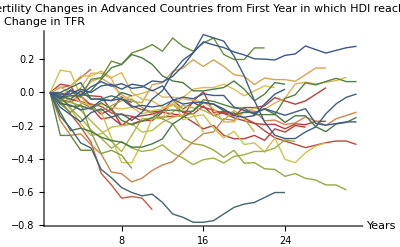

```mathematica
g0 = ListPlot[
Cases[ 
TFRSeriesFromReference[#, bouncethreshold]& /@ advanced, 
(* Eliminate empty series *)
 {_,___}], 
Joined -> True,
PlotStyle -> stylescheme,PlotLabel -> "Total Fertility Changes in Advanced Countries\nfrom First Year in which HDI reaches "<>ToString[bouncethreshold],AxesLabel -> {"Years", "Change in TFR"}]
```

Generate a PNG file containing this chart

```mathematica
Export["FertilitySeries.png", g0, ImageSize -> 420]
```

FertilitySeries.png

Define a function to return a pair of changes, the first being the absolute change in HDI,
the second being the absolute change in TFR, between the reference year and 2005.

```mathematica
ChangeFromReference[country_String, threshold_Real]:=
Module[{refyear = ReferenceYear[country, threshold]},
If[refyear>2005, {Infinity, Infinity},
{HDI[country, 2005]-HDI[country, refyear],
TFR[country, 2005]-TFR[country, refyear]}
]
]
```

Plot these changes in a scatter plot for all advanced countries

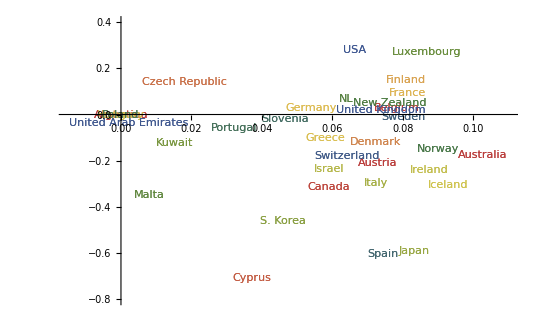

```mathematica
g1 = ListPlot[{ChangeFromReference[#, bouncethreshold]}& /@ advanced, PlotMarkers -> advanced, PlotRange -> {{-0.015, 0.11}, {-0.8, 0.4}},PlotStyle -> stylescheme]
```

The paper fits a model in which countries with HDI above the 0.86 threshold see increasing TFR with increasing HDI, according to which "on average an HDI increase of 0.05 results in an increase of the TFR by 0.204".
Build a plot illustrating this rate of increase for later addition to the plot above.

```mathematica
g2 = ListPlot[{{0,0},{0.1, 0.408}}, Joined -> True, PlotRange -> All, PlotStyle ->  {{Red, Thick, Dashed}}];
```

Define a function to return a complete trajectory of changes in HDI and TFR between the reference year and 2005 (both measured relative to their value in the reference year).

```mathematica
TrajectoryFromReference[country_String, threshold_Real]:=
Module[{refyear = ReferenceYear[country, threshold]},
If[refyear>2005, 
(* Keep non-advanced countries off plots *) 
{{Infinity, Infinity}},
Table[
{HDI[country, y]-HDI[country, refyear],
TFR[country, y]-TFR[country, refyear]}, 
{y, refyear, 2005}]
]
]
```

Build a plot which includes all these trajectories for advanced countries, then display these together with the scatter plot and fitted model plot above

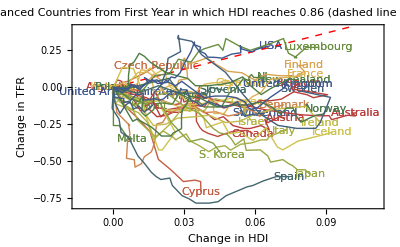

```mathematica
(* Build trajectory plot *)
g3 = ListPlot[
TrajectoryFromReference[#, bouncethreshold]& /@ advanced,  
PlotStyle -> stylescheme,
Joined -> True];
(* Display all three graphs together with nice axes *)
g4 = Show[g1,g2, g3, PlotRange -> {{-0.015, 0.112}, {-0.8, 0.4}},FrameLabel -> {"Change in HDI", "Change in TFR"}, Axes -> True, AxesStyle -> GrayLevel[0.7], Frame -> {{True, False}, {True, False}},PlotLabel -> "Trajectories of Advanced Countries\nfrom First Year in which HDI reaches "<>ToString[bouncethreshold]<>"\n(dashed line is model fitted by the paper)"]
```

Generate a PNG file containing this chart

```mathematica
Export["FertilityTrajectories.png", g4, ImageSize -> 420]
```

FertilityTrajectories.png

## Simulating Bias

Because the reference year is chosen to be the year (within a window) that is lowest, there is a statistical bias for subsequent trajectories to rise.  To investigate this, let's run some simulations.

First though, how long do countries spend in the window?

```mathematica
Select[(ReferenceYear[#, 0.9]-ReferenceYear[#, 0.85])& /@ advanced , 
NumberQ]//Mean//N
```

14.84

Since the entire data set is 30 years, countries spend on average more than half the available time inside the window.  This is plenty of time to create a significant bias by choosing the lowest TFR within the window as the threshold year.

Let's build a simulation to measure how large the bias might be.  For this purpose, we will need to know the mean ("drift") and standard deviation ("vol") of yearly changes in the TFR and HDI.  We will compute these from all advanced countries, for all years in which those countries have an HDI of at least 0.85.  

Define globals TFRDrift and TFRVol by estimation from the data

```mathematica
Block[{changes},
changes = Join@@(Differences[TFRSeriesFromReference[#, 0.85]]&/@ advanced);

TableForm[
{Length[changes],
TFRDrift = Mean[changes], 
TFRVol = StandardDeviation[changes]},
TableHeadings -> {{"Count", "Drift", "Vol"}}
]
]
```

Count | 714
Drift | -0.0100025
Vol | 0.0510942

Notice that the overall mean change in TFR is negative (even though the paper's conclusion implies it should be positive)

Define a function to return the time series of HDI for a given country beginning in its reference year

```mathematica
HDISeriesFromReference[country_String, threshold_Real]:=
If[ReferenceYear[country, threshold]>2005, 
(* Return empty series when HDI never reached threshold *)
{},
Table[HDI[country, y], {y, ReferenceYear[country, threshold], 2005}]
]
```

Define globals HDIDrift and HDIVol by estimation from the data

```mathematica
Block[{changes},
changes = Join@@(Differences[HDISeriesFromReference[#, 0.85]]&/@ advanced);

TableForm[
{Length[changes],
HDIDrift = Mean[changes], 
HDIVol = StandardDeviation[changes]},
TableHeadings -> {{"Count", "Drift", "Vol"}}
]
]
```

Count | 714
Drift | 0.00305163
Vol | 0.00246012

In the simulation, we will generate paths using random walks with the above parameter estimates, in each case beginning where the country was in its reference year.  Let's check when and where the advanced countries were in their reference year

```mathematica
TableForm[SortBy[
{ReferenceYear[#, 0.85], 
TFR[#, ReferenceYear[#, 0.85]],
HDI[#, ReferenceYear[#, 0.85]]}& /@ advanced,
Last], TableHeadings -> {advanced, {"Reference\nYear", "TFR", "HDI"}}]
```

| Reference
Year | TFR | HDI
Argentina | 1979 | 1.48 | 0.850029
Australia | 1988 | 2.17 | 0.85014
Austria | 1995 | 1.29 | 0.850167
Belgium | 1999 | 2.5962 | 0.850206
Canada | 1976 | 1.74 | 0.850449
Cyprus | 1999 | 1.13 | 0.851651
Czech Republic | 1978 | 1.38 | 0.851897
Denmark | 1977 | 2.649 | 0.851992
Estonia | 1980 | 3.242 | 0.851993
Finland | 2002 | 1.24 | 0.852359
France | 1988 | 1.5 | 0.852366
Germany | 1995 | 1.65 | 0.852627
Greece | 1975 | 2.331 | 0.852847
Hungary | 2000 | 2.462 | 0.852974
Iceland | 1978 | 1.87 | 0.853243
Ireland | 1994 | 2.23 | 0.853904
Israel | 1996 | 1.43 | 0.854027
Italy | 1977 | 1.641 | 0.854348
Japan | 2003 | 1.27 | 0.854506
S. Korea | 2001 | 2.6402 | 0.854852
Kuwait | 1975 | 1.736 | 0.8549
Luxembourg | 1976 | 2.529 | 0.855281
Malta | 1975 | 1.688 | 0.855986
NL | 1975 | 1.909 | 0.856136
New Zealand | 1975 | 2.148 | 0.856418
Norway | 2000 | 1.72 | 0.858329
Poland | 1975 | 1.927 | 0.859947
Portugal | 2005 | 1.5 | 0.860467
Slovenia | 1975 | 1.779 | 0.867326
Spain | 1975 | 1.919 | 0.870765
Sweden | 1975 | 1.991 | 0.871365
Switzerland | 1975 | 1.774 | 0.877182
United Arab Emirates | 1975 | 1.598 | 0.878232
United Kingdom | 1975 | 1.664 | 0.881259
USA | 1975 | 1.824 | 0.88653

So most countries are starting near the bottom of the window, and all are within it.

Define a function that takes the development and fertility paths of a country, and implements the threshold finding rule given in the paper with respect to a given window, namely find the lowest value of TFR while the country's HDI is within the window.  Return the position within the path where this lowest value of TFR  is first attained within the window.

```mathematica
FindThreshold[development_List, fertility_List, windowstart_Real, windowend_Real]:=
Module[{eligible, lowestvalue, candidates},

(* Find positions where development is within window *)
eligible= Position[development, d_Real /; (d ≥ windowstart&& d ≤ windowend), {1}];

(* Return last position if there are no eligible ones *)
If[eligible == {}, Return[Length[fertility]]];

(* Determine lowest fertility amongst eligible positions *) 
lowestvalue = Min[Extract[fertility, eligible]];

(* Find positions of this lowest fertility *)
candidates = Position[fertility, lowestvalue, {1}];

(* Return first such position that is eligible *)
First[First[Intersection[candidates, eligible] ]]
]
```

Let's unit test this function by applying it to random series.

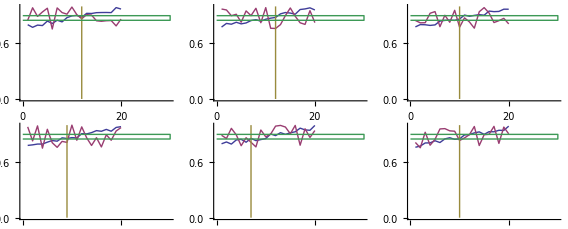

```mathematica
GraphicsGrid[Partition[Table[
Block[{d, f, s},
(* make random development series trending upwards from 0.75 to 1.0 *) 
d = 0.75+RandomReal[0.05, 20]+Range[20]/100;
(* make random fertility series between 0.75 to 1.0 *) 
f = 0.75+RandomReal[0.25, 20];
(* apply function *)
s = FindThreshold[d, f, 0.85, 0.9];
(* display series, found position and window range *)
ListPlot[{d, f, {{s, 0}, {s, 1}}, {{0, 0.85}, {30, 0.85}, {30, 0.9}, {0, 0.9}}}, Joined-> True]
],
{6}],3]]
```

Define a function to generate paths according to a given step distribution.
Note that paths will have (steps+1) elements, the first always being zero;
in this way, the caller can add a constant to change the start value

```mathematica
GeneratePath[distribution_, steps_Integer]:=
Module[{changes},
changes = RandomReal[distribution, steps];
FoldList[Plus, 0, changes]
]
```

Check this function by plotting a few random walk paths with drift 
(use vol of 1 and length of 16, so final standard deviation is 4)

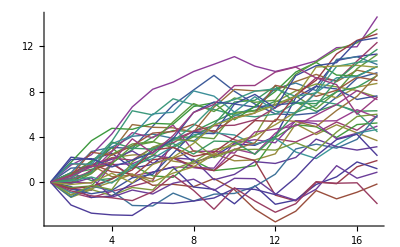

```mathematica
ListPlot[Table[GeneratePath[NormalDistribution[0.5, 1], 16], {40}], Joined -> True]
```

Define a function to generate a path for both development and fertility in the given country, beginning at the values in the country's reference year, but remove the part of the path prior to reaching the HDI threshold according to the paper's definition.  
Return the resulting path as a list of pairs, expressed relative to the starting point.
Let the HDI evolve with drift and vol equal to the overall values for advanced countries found above.   
Let the TFR evolve with vol equal to the overall value for advanced countries found above,
but with zero drift.
Warning: Uses global variables HDIDrift, HDIVol, TFRVol

```mathematica
GeneratePostThresholdPath[country_String, windowstart_Real, windowend_Real] :=
Module[{ y0, f, d, threshold},

(* Find reference year *)
y0 = ReferenceYear[country, windowstart];

(* Generate complete path from reference year *)
d = GeneratePath[NormalDistribution[HDIDrift, HDIVol], 2005-y0]
+HDI[country, y0];
f = GeneratePath[NormalDistribution[0, TFRVol], 2005-y0]
+TFR[country, y0];

(* Determine when country passes threshold according to paper *)
threshold = FindThreshold[d, f, windowstart, windowend];

(* Remove ealier part of path and return as pairs relative to this *)
d = Drop[d, threshold -1];
f = Drop[f, threshold -1];
Transpose[{d-First[d], f-First[f]}]
]
```

Check this function by plotting the resulting trajectories of Australia for a few trials

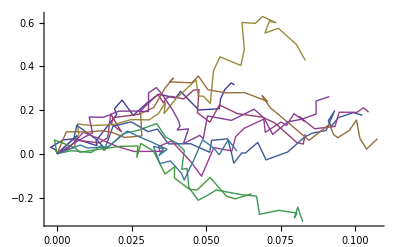

```mathematica
ListPlot[Table[GeneratePostThresholdPath["Australia", 0.85, 0.9], {10}], Joined -> True]
```

Simulate one path for each advanced country, and show these paths with fitted slope from paper

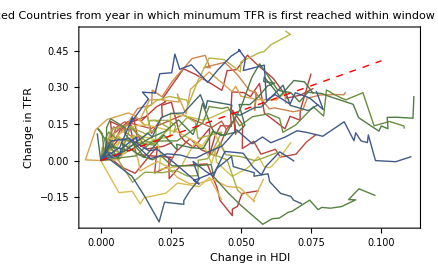

```mathematica
g5 = Show[
ListPlot[Map[GeneratePostThresholdPath[#, 0.85, 0.9]&, advanced], Joined -> True, PlotStyle -> stylescheme], 
g2, 
FrameLabel -> {"Change in HDI", "Change in TFR"}, Axes -> True, AxesStyle -> GrayLevel[0.7], Frame -> {{True, False}, {True, False}},PlotLabel -> "Random Trajectories of Advanced Countries from\nyear in which minumum TFR is first reached within window\n(dashed line is model fitted by the paper)"]
```

```mathematica
Export["FertilitySimulationExample.png", g5, ImageSize -> 420]
```

FertilitySimulationExample.png

So now the fitted slope from the paper looks more plausible, even though we actually generated the data using zero drift in TFR.  Notice that paths tend to have upward trajectories early on -- this is because HDI tends to be still within the window, in which case falls in fertility lead to the threshold being moved.

Now we can measure the size of the bias, at least under this simplified model, by running many such simulations and fitting a relationship between TFR and HDI each time.

Define a function to compute changes in the paths generated above

```mathematica
PathChanges[path_List] :=
If[Length[path]<2, 
{{0,0}},
Transpose[Map[Differences, Transpose[path]]]
]
```

Define a function to sample one path per country and use this to fit a proportional relationship between development and fertility.  Returns the slope of best fit.
Warning: Call to GeneratePostThresholdPath uses global variables HDIDrift, HDIVol, TFRVol

```mathematica
SampleMethod[windowstart_Real, windowend_Real]:=
Module[{allchanges, fit, x},

(* Gather together all the changes in all paths of one run per country *)
allchanges = Join@@Map[
PathChanges[GeneratePostThresholdPath[#, 0.85, 0.9]]&, 
advanced];

(* Use least squares to fit the slope of TFR against HDI *)
fit = Fit[allchanges, x, x];
(* Return slope *)
Coefficient[fit, x]
]
```

The above function effectively simulates the paper's methodology, under a simplified model, in a case where there is no connection between fertility and development at all.
Let's call it 100 times and plot the results.

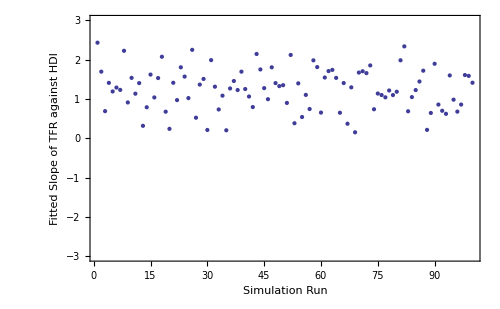

```mathematica
ListPlot[Table[SampleMethod[0.85, 0.9], {100}], 
PlotRange -> {All, {-3,3}},
Axes -> {True, False}, Frame -> {{True, False}, {True, False}},
FrameLabel -> {"Simulation Run", "Fitted Slope of TFR against HDI"}]
```

The bias in the methodology is clear, the resulting fit is almost always above zero, despite the true drift being zero.  Let's look at a historgram of the results, and check the mean and 90% quantile.

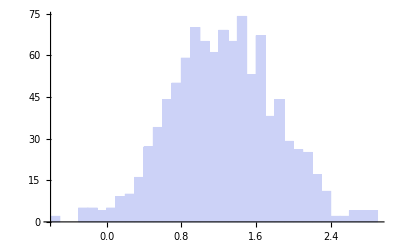

```mathematica
Histogram[sample = Table[SampleMethod[0.85, 0.9], {1000}], {0.1}]
```

```mathematica
{Mean[sample], Quantile[sample, 0.9]}
```

{1.25097,1.96979}

So the typical size of the bias is around 1.25, with values up to 2 being reasonably likely.  However, this is less than the value of 4.08 found in the paper.  So we have only explained half of their result.

For interest, let's check how likely we are to get a zero result from their methdology.

```mathematica
Count[sample, z_/; z≤ 0]/Length[sample]+0.0
```

0.016

So the paper's method only generates the true value or zero, or less, about 1-2% of the time,
and values above 2 about 10% of the time, under this simplified model.

## Panel Model

Let's reproduce the panel analysis done by the authors.  
We first need the set of countries which reach an HDI of 0.85 by 2005.

```mathematica
panelcountries = Select[countrylist, (HDI[#, 2005]≥ 0.85)&];Length[panelcountries]
```

37

Now we need to construct a data set for estimating the following model:
    ΔTFR   =  αΔ B^post + β^preΔ HDI^pre + β^postΔ HDI^post + Δγ + Δυ           (S.3)
which is given as S.3 in the paper's supplementary information at


Under this model, all HDI data is split into pre- and post- threshold values based on a "break year", the year in which the HDI first reaches the threshold in each country.  Accordingly HDI changes always appear in either the second or third term, but never both.

Dummy variables, γ, are used for each year to account for time fixed-effects.  The value of these variables is simply 1 in the corresponding year and 0 otherwise.  Define a function to return all such values for a given year.  Note that since the model works with annual changes in TFR, we don't need a dummy for 1975.

```mathematica
PanelYearDummies[year_Integer] := 
Table[If[i==year, 1, 0], {i, 1976, 2005}];
```

Define a function to return a single data point within the panel.  This comprises the values, for a given country and year, of the variables on the right hand side of S.3 followed by the value of the left hand side.

```mathematica
PanelDataPoint[country_String, year_Integer, threshold_Real]:=
Module[{breakyear = ReferenceYear[country, threshold]},
Join[
{
(* Δ B^post *)
If[year == breakyear, 1, 0],
(* Δ HDI^pre *)
If[year ≥ breakyear, 0, HDI[country, year]-HDI[country, year-1]],
(* Δ HDI^post *)
If[year ≥ breakyear, HDI[country, year]-HDI[country, year-1], 0]
},
(* Δγ *)
PanelYearDummies[year]-PanelYearDummies[year-1],
(* ΔTFR *)
{TFR[country, year]-TFR[country, year-1]}
]
]
```

Define a (self-cacheing) function to collect all available panel data points for a given country.  Again, since the model works in annual changes, no values are computed for 1975.  Also, since some data is missing, the values based on this data need to be removed.

```mathematica
PanelDataSet[country_String, threshold_Real] :=
PanelDataSet[country, threshold] = Select[
(* Generate panel data for every year for this country *)
Table[PanelDataPoint[country, y, threshold], {y, 1976, 2005}],
(* Remove cases where data was missing *)
(Not[MatchQ[#, {_, 0,0,___}]]&&Count[#, _Missing, Infinity]==0)&
]
```

Define a function to estimate the entire panel given a set of country panel data sets.  For later generality, the names of the right hand side variables are passed in as the second argument here.  We enforce a zero intercept since the model is a differences in differences model.  Return the fitted equation in terms of the given right hand side variables.

```mathematica
RunPanel[pointsets_List, RHSvars_List] :=
Module[{model},
(* Standard multiple linear regression with no intercept *)
model = LinearModelFit[Join@@pointsets, RHSvars, RHSvars, IncludeConstantBasis -> False];
model["BestFit"]
]
```

Construct the full data set for all countries in the panel, using a threshold of 0.86 and check its size.

```mathematica
dataset = PanelDataSet[#, 0.86]& /@ panelcountries; Dimensions[Join@@dataset]
```

{1051,34}

So we have 1051 data points (matching that given in the paper) each with 33 right hand side values and 1 left hand side value.

Now run the panel analysis and extract the coefficients for ΔHDI.

```mathematica
fit = RunPanel[dataset, Join[{ΔB, ΔHDIpre, ΔHDIpost}, Array[Δγ, 30]]]
```

-0.00343165 ΔB+4.10179 ΔHDIpost-1.58433 ΔHDIpre-0.0595663 Δγ[1]-0.1107 Δγ[2]-0.16323 Δγ[3]-0.177197 Δγ[4]-0.200026 Δγ[5]-0.25106 Δγ[6]-0.291939 Δγ[7]-0.357986 Δγ[8]-0.396269 Δγ[9]-0.438434 Δγ[10]-0.455855 Δγ[11]-0.477644 Δγ[12]-0.473481 Δγ[13]-0.500128 Δγ[14]-0.496592 Δγ[15]-0.536839 Δγ[16]-0.562577 Δγ[17]-0.61619 Δγ[18]-0.672972 Δγ[19]-0.728081 Δγ[20]-0.750388 Δγ[21]-0.794963 Δγ[22]-0.828084 Δγ[23]-0.854762 Δγ[24]-0.856375 Δγ[25]-0.902439 Δγ[26]-0.931407 Δγ[27]-0.92788 Δγ[28]-0.921002 Δγ[29]-0.942686 Δγ[30]

```mathematica
Coefficient[fit, {ΔHDIpre, ΔHDIpost}]
```

{-1.58433,4.10179}

As can be seen we get results within 1% of those reported in the paper.  This difference may be due to rounding or a different treatment of variance estimation in Mathematica as compared to SAS.

Of particular interest is the increasingly negative fitted coefficient for the Δγ, the year dummies.  This means that the model is expecting substantial decreases in TFR if HDI does change.

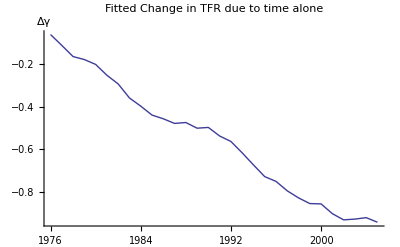

```mathematica
g5 = ListPlot[
Transpose[{Range[1976, 2005],Coefficient[ fit, Array[Δγ, 30]]}], Joined -> True, PlotLabel -> "Fitted Change in TFR due to time alone", AxesOrigin ->  {1975, 0}, AxesLabel -> {None, "Δγ"}]
```

Generate a PNG file containing this chart

```mathematica
Export["FertilityYearDummies.png", g5, ImageSize -> 350]
```

FertilityYearDummies.png

Simply moving from the year 1982 into 1983 is estimated to reduce fertility by 0.066, or 4 children per 15 mothers.

```mathematica
Coefficient[ fit, Δγ[1983-1975]]-Coefficient[ fit, Δγ[1982-1975]]
```

-0.0660473

So countries whose TFR doesn't change at all will be seen by the model as increasing relative to this expected fall.  What the panel result tells us is not that highly advanced countries have increasing fertility, but that these countries' fertility falls less fast than that of less advanced countries.

The trouble seems to be that the time-fixed affects are estimated using some data when countries are below the threshold, but then applied to countries that are above the threshold.  Poland spends 30 out of the 31 years below the threshold, with falling fertility during most of this time.  These falls in fertility are used by the model to estimate the time fixed-effects, such as the fertility reduction of 0.066 in associated with 1982.  These effects are then applied as a base-line to highly developed countries.

Let's see how many countries are still below the threshold in 1982

```mathematica
Count[(HDI[#, 1982]&  /@ panelcountries), x_/; x<0.85]
```

12

So twelve of the countries used in the panel are still below the threshold in 1982, and these contribute to the result that fertility decreases so much between 1982 and 1983 according to the model.  But are these countries really relevant to the time fixed-effects in countries above the threshold?  Surely whatever it is that causes these less developed countries to have falling rather than rising fertility would also cause the year 1982 to have a different impact on these countries as on more developed ones too.

Let's reduce the set of countries in the panel so as to include only more developed countries (and thus less data from countries below the threshold) by only selecting countries that make it to an HDI of 0.89.  We'll still use a threshold of 0.86 for the model, but simply apply it to fewer countries.

```mathematica
advancedpanelcountries = Select[countrylist, (HDI[#, 2005]≥ 0.89)&];Length[advancedpanelcountries]
```

27

The reduced set of countries is still most of the original 37.  What countries are still included?

```mathematica
advancedpanelcountries
```

{Australia,Austria,Belgium,Canada,Cyprus,Denmark,Finland,France,Germany,Greece,Iceland,Ireland,Israel,Italy,Japan,S. Korea,Luxembourg,NL,New Zealand,Norway,Portugal,Slovenia,Spain,Sweden,Switzerland,United Kingdom,USA}

These are all developed countries, except perhaps Cyprus and Portugal.  What countries have we removed?

```mathematica
Complement[panelcountries, advancedpanelcountries]
```

{Argentina,Chile,Czech Republic,Estonia,Hungary,Kuwait,Malta,Poland,Slovak Republic,United Arab Emirates}

These are all developing countries, or recently borderline developed ones, which we could reasonably expect to behave very differently from the developed ones above.  Let's run the reduced panel.

```mathematica
reducedfit = RunPanel[PanelDataSet[#, 0.86]& /@ advancedpanelcountries, Join[{ΔB, ΔHDIpre, ΔHDIpost}, Array[Δγ, 30]]]
```

-0.00636293 ΔB-0.0724818 ΔHDIpost-6.14628 ΔHDIpre-0.0503438 Δγ[1]-0.0950232 Δγ[2]-0.127193 Δγ[3]-0.114552 Δγ[4]-0.114466 Δγ[5]-0.154709 Δγ[6]-0.1841 Δγ[7]-0.245232 Δγ[8]-0.26884 Δγ[9]-0.304757 Δγ[10]-0.305197 Δγ[11]-0.311616 Δγ[12]-0.284688 Δγ[13]-0.286954 Δγ[14]-0.252455 Δγ[15]-0.274879 Δγ[16]-0.268127 Δγ[17]-0.294721 Δγ[18]-0.309181 Δγ[19]-0.333302 Δγ[20]-0.334397 Δγ[21]-0.34757 Δγ[22]-0.355937 Δγ[23]-0.357067 Δγ[24]-0.338454 Δγ[25]-0.373646 Δγ[26]-0.38272 Δγ[27]-0.360785 Δγ[28]-0.340017 Δγ[29]-0.351333 Δγ[30]

```mathematica
Coefficient[reducedfit, {ΔHDIpre, ΔHDIpost}]
```

{-6.14628,-0.0724818}

So suddenly the key result of the paper disappears.  Now increasing HDI mildly reduces fertility.  Yes, the rate of decrease is less than for countries below the threshold.  But there is no longer an increase.  The alleged reversal in fertility declines doesn't exist at all unless we use data from the developing countries to estimate time fixed-effects for developed countries.

Let's look at the time fixed-effects in our reduced panel

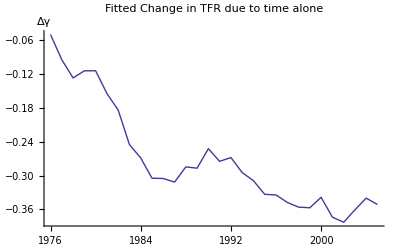

```mathematica
ListPlot[Transpose[{Range[1976, 2005],Coefficient[ reducedfit, Array[Δγ, 30]]}], Joined -> True, PlotLabel -> "Fitted Change in TFR due to time alone", AxesOrigin ->  {1975, 0}, AxesLabel -> {None, "Δγ"}]
```

We still seem to have a downward trajectory for the time fixed-effects, but it is no where near as steep.  This is why the result for the impact of HDI is no longer strongly positive.

Let's see what happens if we include all countries from the entire original database in the panel.

```mathematica
globalfit = RunPanel[PanelDataSet[#, 0.86]& /@ countrylist, Join[{ΔB, ΔHDIpre, ΔHDIpost}, Array[Δγ, 30]]];
Coefficient[globalfit, {ΔHDIpre, ΔHDIpost}]
```

{-0.588974,10.8771}

So using even the most under-developed countries, whose fertilities are all falling rapidly, generates an even larger positive impact for HDI.  Should we then conclude that fertility increases 2.6 times faster than the paper concludes?  After all, we've simply thrown in more countries; surely that could only make the result more statistically significant?  No, the problem is that the methodology is wrong.

Here's another way to look at it.  Suppose we build a simplified model where the the pre-threshold data isn't used at all.  To do this, we simply need to remove the second term of S.3.

```mathematica
(* Delete panel points with 0 for ΔHDIpost, i.e. those with non-zero ΔHDIpre *)
postonlydataset = DeleteCases[#, {_, _, 0, ___}]& /@ dataset;
(* Remove the ΔHDIpre values from all points -- these are now zero anyway *)
postonlydataset = Map[Drop[#, {2,2}]& , postonlydataset, {2}];
Dimensions[Join@@postonlydataset]
```

{658,33}

Rerun the panel using this simplified model (note that Δ HDI^pre no longer appears in the right hand side variables list).

```mathematica
postonlyfit = RunPanel[postonlydataset, Join[{ΔB, ΔHDIpost}, Array[Δγ, 30]]];
Coefficient[postonlyfit, ΔHDIpost]
```

-0.846856

So again, the fertility decreases with increasing HDI.  We don't see any of the claimed reversal of the fertility declines.

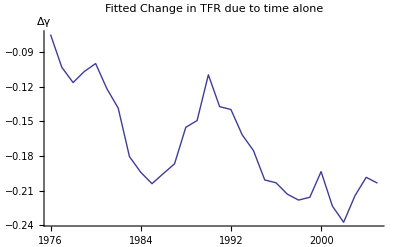

```mathematica
ListPlot[Transpose[{Range[1976, 2005],Coefficient[ postonlyfit, Array[Δγ, 30]]}], Joined -> True, PlotLabel -> "Fitted Change in TFR due to time alone", AxesOrigin ->  {1975, 0}, AxesLabel -> {None, "Δγ"}]
```

Also the time fixed-effects exhibit almost no decrease, indicating a much more satisfactory model.

## Null Model Trajectories

Let's explore the null hypothesis being proposed in the model when testing for the statistical significance of β^post.

Define a function to return the value of ΔTFR for a given country and year using S.3 and the estimated fit but with Δ HDI^post set to zero; that is, the null hypothesis value.
Warning: this version only handles cases where Δ HDI^pre is zero, that is cases where the country is at or beyond its reference year and hence above the HDI threshold

```mathematica
NullModelPredictionPoint[country_String, year_Integer, threshold_Real, fit_]:=
Module[{values, breakyear = ReferenceYear[country, threshold]},
(* Compute values for RHS variables at this country & year *)
values = Join[
{ΔB -> If[year == breakyear, 1, 0], 
ΔHDIpre -> 0,    (* assume country has passed HDI threshold *)
ΔHDIpost -> 0, (* set HDI response to zero *) 
Δγ[year-1975]-> 1, 
Δγ[year-1976]-> -1},
(* all other year dummy changes are zero *)
MapThread[Rule, {Table[Δγ[i], {i, 1, 30}], Table[0, {30}]}]
];
(* Replace RHS variables with their values in fitted equation *)
fit /. values
]
```

Define a function to return the null hypothesis series for TFR for a given country from its reference year until 2005 from the estimated fit.  Successive TFR values expressed as differences from TFR in reference year.

```mathematica
NullModelPredictionSeries[country_String, threshold_Real, fit_] := 
Module[{changes},
(* Compute changes in every year after reference year *)
changes = Table[
NullModelPredictionPoint[country, y, threshold, fit], {y, ReferenceYear[country, threshold]+1, 2005}
];
(* Return cumulative sums of changes *)
FoldList[Plus, 0, changes]
]
```

Define a function to return the series of pairs of HDI and TFR changes for a given country under the null hypothesis.  HDI values are simply the observed changes from the reference year, while the TFR values used the fitted model with  Δ HDI^post set to zero.

```mathematica
NullModelTrajectory[country_String, threshold_Real, fit_] :=
Module[{refyear = ReferenceYear[country, threshold]},
Transpose[{
Table[HDI[country, y]-HDI[country,refyear], {y, refyear, 2005}],
NullModelPredictionSeries[country, threshold, fit]
}]
]
```

Build a plot of the total changes in HDI and TFR under the null hypothesis from the reference year of all advanced countries, using the countries' names as labels.

```mathematica
g6 = ListPlot[{Last[NullModelTrajectory[#, bouncethreshold, fit]]}& /@ advanced, PlotRange -> {{-0.015, 0.112}, {-1.1, 0.1}}, PlotMarkers -> advanced,PlotStyle -> stylescheme];
```

Build a plot of the trajectories of HDI and TFR under the null hypothesis beginning in the reference year for all advanced countries.

```mathematica
g7 = ListPlot[
NullModelTrajectory[#, bouncethreshold, fit]& /@ advanced, 
Joined -> True,
PlotStyle -> stylescheme
];
```

Display the above two plots together with nice axes

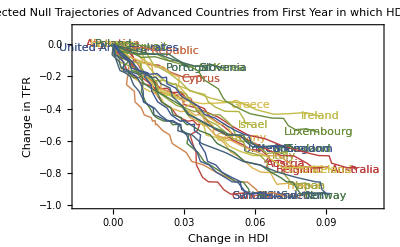

```mathematica
g8 = Show[{g6, g7}, PlotRange -> {{-0.015, 0.112}, {-1, 0.1}},FrameLabel -> {"Change in HDI", "Change in TFR"}, Axes -> {True, True}, AxesOrigin -> {0,0}, AxesStyle -> GrayLevel[0.7], Frame -> {{True, False}, {True, False}},PlotLabel -> "Projected Null Trajectories of Advanced Countries\nfrom First Year in which HDI reaches "<>ToString[bouncethreshold]]
```

Generate a PNG file containing this chart

```mathematica
Export["FertilityNullTrajectories.png", g8, ImageSize -> 420]
```

FertilityNullTrajectories.png

Find those countries whose null trajectories finish below 1.0

```mathematica
TableForm[SortBy[
Cases[{#, TFR[#, ReferenceYear[#, 0.86]]+Last[Last[NullModelTrajectory[#, bouncethreshold, fit]]]}& /@ advanced, 
{_, x_ /; x < 1}],
Last]]
```

Switzerland | 0.655314
NL | 0.721314
Germany | 0.7453
USA | 0.831314
Sweden | 0.836314
Finland | 0.872544
Austria | 0.87734
Canada | 0.881314
Luxembourg | 0.883583
Belgium | 0.911544
Italy | 0.925374
France | 0.94488
Japan | 0.96688
Denmark | 0.976314
Greece | 0.999891

## Varying Countries Included In Panel

Let's explore varying the inclusion criteria for the panel.

Define a function to run a panel over all countries whose 2005 HDI score is above the given qualification level, and return β^post in the resulting fit.  Make it self-cacheing.  
Warning: Uses the global variable countrylist 
Note: Also uses global symbols for right hand side variables: B, ΔHDIpre, ΔHDIpost, Δγ[Range[30]]

```mathematica
PanelByDevelopment[qualification_Real, threshold_Real]:=
Module[{panellist, fit},
panellist = Select[countrylist, (HDI[#, 2005]≥ qualification)&];
fit = RunPanel[PanelDataSet[#, threshold]& /@ panellist, Join[{ΔB, ΔHDIpre, ΔHDIpost}, Array[Δγ, 30]]];
Coefficient[fit, ΔHDIpost]
]
```

Define a wrapper function that calls and caches the above function, but first shifts the given qualification score up to the next score that exactly equals that of at least one country in 2005.   Uses a helper function that maps from arbitrary HDI scores to ones that are present for at least one country in 2005.
Warning: Uses the global variable countrylist

```mathematica
(* Define helper function *)
FastPanelByDevelopmentMapping = Block[{sortedHDIvalues},
(* Sort all actual HDI scores in 2005 *)
sortedHDIvalues = Sort[
DeleteCases[HDI[#, 2005]& /@ countrylist, _Missing]
];
(* Create a map from arbitrary HDI scores 
to the next higher or equal available one *)
Interpolation[Transpose[{#,#}&[sortedHDIvalues]], InterpolationOrder->0]
];
(* Define self-cacheing main function *)
FastPanelByDevelopment[qualification_Real, threshold_Real] :=
FastPanelByDevelopment[qualification, threshold] = 
PanelByDevelopment[
(* Suppress extrapolation warnings from mapping *)
Quiet[
FastPanelByDevelopmentMapping[qualification],{InterpolatingFunction::"dmval"}
], 
threshold
];
```

Define a function that returns the graphics commands required to place a point on the chart below with a label giving the number of countries that are included for the given qualification level of HDI.

```mathematica
SpotMarking[qualification_Real, threshold_Real, colour_] :=
Module[{h, c, n},
(* Find the next equal or higher available HDI score to the given qualification level*) 
h = Quiet[
FastPanelByDevelopmentMapping[qualification],{InterpolatingFunction::"dmval"}];
(* Determine the panel result using this HDI level as qualification *)
c = FastPanelByDevelopment[h, threshold];
(* Count the number of countries that qualify *)
n = Count[countrylist, x_ /;(HDI[x, 2005]≥ qualification)];
(* Generate a labelled point in the given colour *)
{Gray, Inset[ToString[n], {h+0.01, c+0.5}],colour, PointSize[Medium],Point[{h, c}]}
]
```

Create a chart showing how the panel result changes as the number of countries included in the panel varies.  Note: This will take a while to run the first time it is executed, since it needs to run the entire model more than 80 times.

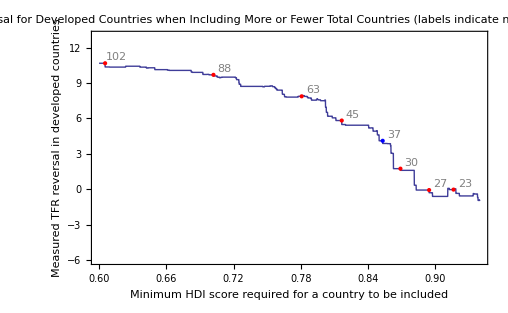

```mathematica
g9 = Plot[FastPanelByDevelopment[h, bouncethreshold], {h, 0.6, 0.94}, PlotRange -> {All, {-6, 13}}, Frame -> {{True, False}, {True, False}},
PlotLabel -> "Measured Reversal for Developed Countries when\nIncluding More or Fewer Total Countries\n(labels indicate number of countries included)",FrameLabel -> {"Minimum HDI score required for a country to be included", "Measured TFR reversal in developed countries"}, 
Epilog -> Join[SpotMarking[#, bouncethreshold, Red]& /@ {0.6, 0.7, 0.78, 0.815, 0.868, 0.89, 0.915},
SpotMarking[0.85, bouncethreshold, Blue]]
]
```

Generate a PNG file containing this chart

```mathematica
Export["FertilityInclusionCriteria.png", g9, ImageSize -> 420]
```

FertilityInclusionCriteria.png